```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
<<Superradiance`
```

Superradiance package

```mathematica
ph=PhaseDeltaFormat@SolveMode[0.7,-2,2,2,0.3,IncreasePrecision,"Parallelize"->False,"Verbose"->True];
```

𝒥=0.7, ℓ=2, ω̄=0.3 (1.09 sec)

```mathematica
ArgParse=#-Accumulate@Join[{0},2π Boole@Thread[Abs[#⟦1;;-2⟧-#⟦2;;All⟧]>0.85Pi]]&;
```

```mathematica
dif=ArcTan@@@ph[[All,{6,7}]]-2Arg@Gamma[ph[[All,3]]+1-(2 ph[[All,5]])/(1+√(1-ph[[All,1]]^2))I]
```

{0.765018,0.470935,0.389421,0.351399,0.329512,0.31533,0.305409,0.298087,0.292464,0.288013,0.284402,0.281416,0.278904,0.276763,0.274917,0.273308,0.271893,0.27064,0.269523,0.26852,0.267614,0.266793,0.266044,0.26536,0.26473,0.264152,0.263614,0.263121,0.262655,0.262229,0.26182,0.261451,0.261088,0.260767,0.260439,0.260161,0.259859,0.259621,0.259338,0.259137,0.258865,0.258703,0.258432,0.258311,0.258034,0.257957,0.257663,0.257637,0.257315,0.257349,0.256986,0.25709,0.25667,0.256858,0.256363,0.256654,0.256062,0.256475,0.255761,0.256322}

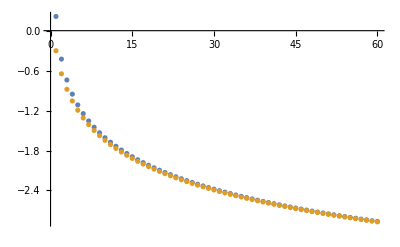

```mathematica
{ArcTan@@@ph⟦All,{6,7}⟧-First@LinearModelFit[ArcTan@@@ph⟦All,{6,7}⟧-2Arg@Gamma[ph⟦All,3⟧+1-(2 ph⟦All,5⟧)/(1+√(1-ph⟦All,1⟧^2))I],Table[l^-i,{i,0,2}],l]["BestFitParameters"],2Arg@Gamma[ph[[All,3]]+1-(2 ph[[All,5]])/(1+√(1-ph[[All,1]]^2))I]}//ListPlot
```

```mathematica
ph0=Table[PhaseDeltaFormatBoth@SolveMode[0.7,-1,ℓ,𝓂,0.3,IncreasePrecision,"Parallelize"->False,"Verbose"->True],{ℓ,1,50},{𝓂,-ℓ,ℓ}];
```

```mathematica
ph=ph0//Flatten[#,1]&
```

{{0.7,-1,1,-1,0.3,0.701499,0.587903},{0.7,-1,1,0,0.3,0.828737,0.530781},2596,{0.7,-1,50,49,0.3,-0.79514,-0.606581},{0.7,-1,50,50,0.3,-0.795161,-0.606554}}
 |  |  |  |

```mathematica
ph//KeyValueMap[Thread@*List]@GroupBy[#,(#[[3]]&)->(ArcTan[#[[6]],#[[7]]]&)]&//ListPlot[#,PlotRange->Full]&
```

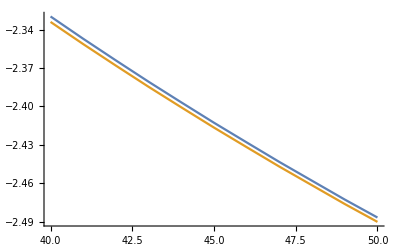

```mathematica
ph//Through/@{First,Last}/@GroupBy[#,(#[[3]]&)->(ArcTan[#[[6]],#[[7]]]&)]&//Transpose@*KeyValueMap[Thread@*List]//ListPlot[#[[All,40;;]],Joined->True]&
```

```mathematica
First@LinearModelFit[dif,Table[l^-i,{i,0,2}],l]["BestFitParameters"]
```

0.249748

```mathematica
nlmf["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
α | 0.244027 | 0.000986879 | 247.272 | 2.19728×10^-89
β | 0.493546 | 0.00599043 | 82.3891 | 8.54975×10^-62

```mathematica
Table[Sign[x]+1,{x,-2,2}]
```

{0,0,1,2,2}

```mathematica
25.+25.*(Sign[x]-1)/2
```

25.+12.5 (-1+Sign[x])

```mathematica
Floor[25/10]
```

2